```mathematica
Cities = Import[
"https://github.com/hflabs/city/raw/ae661bffe572880472249097c9b29c42b09650ea/city.csv", {"CSV", "Dataset"}, HeaderLines -> 1][
All, {"address", "city", "geo_lat", "geo_lon", "population"}][
SortBy[-#population&]][
1;;30] // 
Map[Append[#,
"city" -> If[
#["city"] == "",
StringDrop[#["address"], 2], 
#["city"]
]
]&
]
```

```mathematica
CityPositions = Normal[GeoPosition[{#["geo_lat"], #["geo_lon"]}]& /@Cities];
CityNames = Normal[#["city"]& /@ Cities];
CityCount = Length[Cities];
```

```mathematica
GeoDistance[CityPositions[[1]], CityPositions[[2]]]
```

636.023 km

```mathematica
CircuitPairs[p_]:=Module[{step},
step[{d_, old_}, new_]:={Append[d,{old,new}],new};
Fold[step, {{},p[[-1]]}, p][[1]]
]

CircuitPairs[{1,2,3}]
```

{{3,1},{1,2},{2,3}}

```mathematica
CircuitDistance[p_]:=Module[{step},
step[{d_, old_}, new_]:={d+GeoDistance[CityPositions[[old]],CityPositions[[new]]],new};
Fold[step, {0,p[[-1]]}, p][[1]]
]

UnitConvert[CircuitDistance[{1, 2, 3, 4, 5, 6}],"Kilometers"]
UnitConvert[CircuitDistance[Range[CityCount]],"Kilometers"]
```

7217.34 km

65368.5 km

```mathematica
UpdateCircuit[p_]:=Module[{a,b},
a = RandomInteger[{1,Length[p]}];
b = RandomInteger[{1,Length[p]}];
If[a == b,
UpdateCircuit[p],
ReplacePart[p,{a->p[[b]], b-> p[[a]]}]
]
]

UpdateCircuit[Range[3]]
```

{2,1,3}

```mathematica
Options[Annealing] = {"InitialTemperature" -> 60000., "FinishTemperature" -> 80, "CoolingFactor" -> 0.95};
Annealing[OptionsPattern[]]:=Module[{ C, Te, prop, step},
C = OptionValue["CoolingFactor"];
Te = OptionValue["FinishTemperature"];
prop[x_, T_]:= Exp[-
QuantityMagnitude[
UnitConvert[
CircuitDistance[x],
"Kilometers"
] 
]/T];
step[{T_, x_}]:= Module[{x1,α, u},{
T*C, 
(
(*Print[T, x];*)
x1=UpdateCircuit[x];
α=prop[x1, T] / prop[x, T];
u=RandomReal[];
If[u≤α,x1,x]
)
}];

NestWhileList[step,{
OptionValue["InitialTemperature"],
RandomSample[Range[CityCount]]
},#[[1]]>Te&]
]

(*Annealing[InitialTemperature -> 200, CoolingFactor -> 0.99]*)
```

```mathematica
AnnealingTime = Timing[Results = <|
"slow"-> Annealing[CoolingFactor -> 0.90],
"middle"-> Annealing[CoolingFactor -> 0.95],
"fast"-> Annealing[CoolingFactor -> 0.99]
|>][[1]];

StringForm["Finished the simulated annealing in ``s", AnnealingTime]
```

Finished the simulated annealing in 9.45638s

```mathematica
Distances[h_]:= CircuitDistance[#[[2]]]& /@ h;

ResultDistances = Distances[#]& /@ Results;
```

```mathematica
ResultTemperatures = (#[[1]]&/@ #)&/@Results;
```

```mathematica
UnitConvert[#[[-1]], "Kilometers"]& /@ ResultDistances
```

<|slow→40213.4 km,middle→42154.4 km,fast→25085.6 km|>

```mathematica
(* Taken from https://mathematica.stackexchange.com/questions/627/1-plot-2-scale-axis *)
TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=Last[PlotRange/.AbsoluteOptions[#,PlotRange]]&/@{fgraph,ggraph};
fticks=Last[Ticks/.AbsoluteOptions[fgraph,Ticks]]/._RGBColor|_GrayLevel|_Hue:>ColorData[1][1];
gticks=(MapAt[Function[r,Rescale[r,grange,frange]],#,{1}]&/@Last[Ticks/.AbsoluteOptions[ggraph,Ticks]])/._RGBColor|_GrayLevel|_Hue->ColorData[1][2];
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Transparent}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]

TwoAxisListLinePlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListLinePlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=Last[PlotRange/.AbsoluteOptions[#,PlotRange]]&/@{fgraph,ggraph};
fticks=Last[Ticks/.AbsoluteOptions[fgraph,Ticks]]/._RGBColor|_GrayLevel|_Hue:>ColorData[1][1];
gticks=(MapAt[Function[r,Rescale[r,grange,frange]],#,{1}]&/@Last[Ticks/.AbsoluteOptions[ggraph,Ticks]])/._RGBColor|_GrayLevel|_Hue->ColorData[1][2];
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Transparent}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

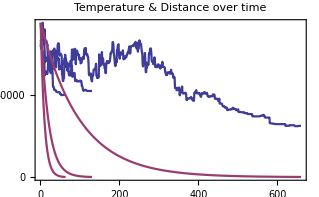

```mathematica
Show[
TwoAxisListLinePlot[{ResultDistances, ResultTemperatures}],
PlotLabel->"Temperature & Distance over time",
LabelStyle->{FontFamily->"Fira Sans"}
]
```

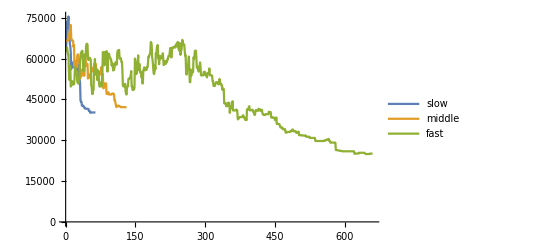

```mathematica
ListPlot[ResultDistances,Joined->True]
```

```mathematica
PlotState[{T_,p_}]:=(
Overlay[{
GeoGraphPlot[
DirectedEdge @@(CityPositions[[#]]&/@#)&/@ CircuitPairs[p],
(*VertexLabels->(Map[CityPositions[[#]]-> CityNames[[#]]&,Range[CityCount]]),*)
GraphLayout->"Geodesic",
GeoBackground->"VectorClassic"
]
}]
)

PlotState[Results[["slow"]][[1]]]
PlotState[Results[["fast"]][[-1]]]
```

-Graphics-

-Graphics-

```mathematica
Frames =(PlotState/@Results[["fast"]]);
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

Export::errframe: PlotState cannot be converted to an expression suitable for video export.

```mathematica
Export["animation.avi",Frames, BitRate->1000000, RasterSize->1920];
```